## Profile Generation

### Sigmoidal Function

```mathematica
c[z_]:=1/(1+Exp[-z])
```

### Interpolating Dielectric Profile - Dimensionless Grouped

```mathematica
qSubs=Collect[q->r c[s]+c[a]-(r+1)c[-a],r,Simplify]
```

q→(-1+ⅇ^a)/(1+ⅇ^a)+(-1/(1+ⅇ^a)+1/(1+ⅇ^-s)) r

```mathematica
odeXsDG=0==Collect[(Ex''[s]+(q Ω^2)/(c[a]-c[-a])Ex[s])/.qSubs,{Ex[s],Ex''[s]},Simplify]
```

0==((-1+ⅇ^a-ⅇ^s-r+ⅇ^(a+s) (1+r)) Ω^2 Ex[s])/((-1+ⅇ^a) (1+ⅇ^s))+Ex''[s]

```mathematica
JoinedScalesSubs={r->δ^α,a->δ^β,s->ξ δ^β,Ω->δ^γ,Ex[s]->Ex[ξ],Ex''[s]->δ^(-2β)  Ex''[ξ]}
```

{r→δ^α,a→δ^β,s→δ^β ξ,Ω→δ^γ,Ex[s]→Ex[ξ],Ex''[s]→δ^(-2 β) Ex''[ξ]}

```mathematica
odeXξJS=Collect[Expand[δ^(2β)odeXsDG[[2]]/.JoinedScalesSubs],{Ex[ξ],Ex''[ξ]},Simplify]
```

(δ^(2 (β+γ)) (-1+ⅇ^(δ^β)-ⅇ^(δ^β ξ)-δ^α+ⅇ^(δ^β (1+ξ)) (1+δ^α)) Ex[ξ])/((-1+ⅇ^(δ^β)) (1+ⅇ^(δ^β ξ)))+Ex''[ξ]

## Thin layer Approximation

```mathematica
Q=Coefficient[odeXsDG[[2]]/Ω^2,Ex[s]]
```

(-1+ⅇ^a-ⅇ^s-r+ⅇ^(a+s) (1+r))/((-1+ⅇ^a) (1+ⅇ^s))

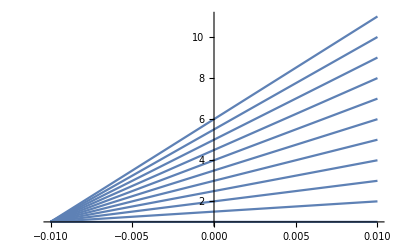

```mathematica
Plot[Table[Q/.a->0.01,{r,0,10}],{s,-0.01,0.01}]
```

```mathematica
QasSmall=Collect[Series[Coefficient[odeXsDG[[2]]/Ω^2,Ex[s]],{s,0,1},{a,0,1}],a,Simplify]
```

(2+r)/2+(r s)/(2 a)+(a r s)/24

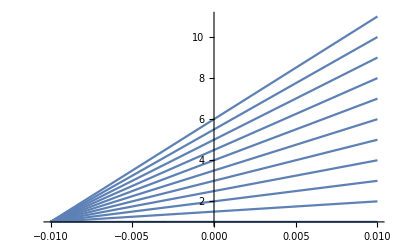

```mathematica
Plot[Table[QasSmall/.a->0.01,{r,0,10}],{s,-0.01,0.01}]
```

```mathematica
QasSmallApx=Collect[(2+r)/2+(r s)/(2 a),r]
```

1+r (1/2+s/(2 a))

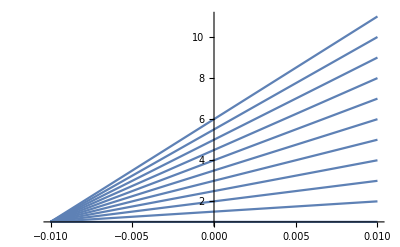

```mathematica
Plot[Table[QasSmallApx/.a->0.01,{r,0,10}],{s,-0.01,0.01}]
```

```mathematica
QasSmallApxJS=Collect[QasSmallApx/.JoinedScalesSubs,δ^α]
```

1+δ^α (1/2+ξ/2)

```mathematica
TeXForm[odeXsJSapx]
```

\text{Ex}''(\xi )+\text{Ex}(\xi ) \left(\left(\frac{\xi }{2}+\frac{1}{2}\right) \delta ^{\alpha
   }+1\right) \delta ^{2 (\beta +\gamma )}=0

```mathematica
odeXsJSapx=Ex''[ξ]+QasSmallApxJS δ^(2(β+γ))Ex[ξ]==0
```

δ^(2 (β+γ)) (1+δ^α (1/2+ξ/2)) Ex[ξ]+Ex''[ξ]==0

#### Prototype Equations

α > 0, β + γ >= O (1) : Ex''[ξ] = 0

α>0 ,|β+γ|<<1: regular perturbation

α>0, β+γ<0: WKB  δ^(2 (β+γ))  Ex[ξ]+Ex''[ξ]==0

α < 0, | β + γ | << 1, α + 2 (β + γ) > 0 : regular perturbation

α < 0, β + γ < -O (1) : singular problem

### WKB Error Term

```mathematica
S2Func[Q_]:=Integrate[D[Q,ξ,ξ]/(8 Q^(3/2))-(5 D[Q,ξ]^2)/(32 Q^(5/2)),ξ]
```

```mathematica
ThinLayerError = δ^γ S2Func[(1+δ^α (1/2+ξ/2))]
```

(5 δ^(α+γ))/(24 √2 (2+δ^α+δ^α ξ)^(3/2))

```mathematica
TeXForm[ThinLayerError]
```

\frac{5 \delta ^{\alpha +\gamma }}{24 \sqrt{2} \left(\xi  \delta ^{\alpha }+\delta ^{\alpha
   }+2\right)^{3/2}}

## Regular Perturbation Formal Expansions - Thin Layer

```mathematica
odeThinXs=Ex''[s]+Ω^2 QasSmallApx Ex[s]==0
```

(1+r (1/2+s/(2 a))) Ω^2 Ex[s]+Ex''[s]==0

```mathematica
ExRegularSubs={Ex[s]->Ex0[s]+r Ex1[s],Ex''[s]->Ex0''[s]+r Ex1''[s]}
```

{Ex[s]→Ex0[s]+r Ex1[s],Ex''[s]→Ex0''[s]+r Ex1''[s]}

```mathematica
odeThinXsPer=odeThinXs/.ExRegularSubs
```

(1+r (1/2+s/(2 a))) Ω^2 (Ex0[s]+r Ex1[s])+Ex0''[s]+r Ex1''[s]==0

```mathematica
odeThinXsPer0=Coefficient[odeThinXsPer[[1]],r,0]
```

Ω^2 Ex0[s]+Ex0''[s]

```mathematica
odeThinXsPer1=Coefficient[odeThinXsPer[[1]],r,1]
```

1/2 Ω^2 Ex0[s]+(s Ω^2 Ex0[s])/(2 a)+Ω^2 Ex1[s]+Ex1''[s]

```mathematica
TeXForm[-Simplify[Coefficient[odeThinXsPer1,Ex0[s]]]]
```

-\frac{\Omega ^2 (a+s)}{2 a}

```mathematica
SolThinXsPer0=Ex0[s]->C[1]Exp[-I Ω s]+C[2]Exp[I Ω s]
```

Ex0[s]→ⅇ^(-ⅈ s Ω) C[1]+ⅇ^(ⅈ s Ω) C[2]

```mathematica
SolThinXsPer0=DSolve[0==odeThinXsPer1/.SolThinXsPer0,Ex1[s],s][[1]]
```

{Ex1[s]→C[3] Cos[s Ω]+C[4] Sin[s Ω]-1/(16 a Ω)ⅈ ⅇ^(-2 ⅈ s Ω) (-C[1] Cos[s Ω]-2 ⅈ a Ω C[1] Cos[s Ω]-2 ⅈ s Ω C[1] Cos[s Ω]+4 a ⅇ^(2 ⅈ s Ω) s Ω^2 C[1] Cos[s Ω]+2 ⅇ^(2 ⅈ s Ω) s^2 Ω^2 C[1] Cos[s Ω]+ⅇ^(4 ⅈ s Ω) C[2] Cos[s Ω]-2 ⅈ a ⅇ^(4 ⅈ s Ω) Ω C[2] Cos[s Ω]-2 ⅈ ⅇ^(4 ⅈ s Ω) s Ω C[2] Cos[s Ω]-4 a ⅇ^(2 ⅈ s Ω) s Ω^2 C[2] Cos[s Ω]-2 ⅇ^(2 ⅈ s Ω) s^2 Ω^2 C[2] Cos[s Ω]-ⅈ C[1] Sin[s Ω]+2 a Ω C[1] Sin[s Ω]+2 s Ω C[1] Sin[s Ω]-4 ⅈ a ⅇ^(2 ⅈ s Ω) s Ω^2 C[1] Sin[s Ω]-2 ⅈ ⅇ^(2 ⅈ s Ω) s^2 Ω^2 C[1] Sin[s Ω]-ⅈ ⅇ^(4 ⅈ s Ω) C[2] Sin[s Ω]-2 a ⅇ^(4 ⅈ s Ω) Ω C[2] Sin[s Ω]-2 ⅇ^(4 ⅈ s Ω) s Ω C[2] Sin[s Ω]-4 ⅈ a ⅇ^(2 ⅈ s Ω) s Ω^2 C[2] Sin[s Ω]-2 ⅈ ⅇ^(2 ⅈ s Ω) s^2 Ω^2 C[2] Sin[s Ω])}

## WKB Formal Expansion - Thin Layer

We cannot integrate QaSmallApx directly because it is a linear function with slope r << 1: inverse not bounded. We must first expand to series.

```mathematica
PhaseSer=Normal[Series[Sqrt[QasSmallApx],{r,0,1}]]
```

1+(r (a+s))/(4 a)

```mathematica
WKBThinLayer=PhaseSer^(-1/4)Exp[Integrate[I Ω PhaseSer,s]]
```

(ⅇ^(ⅈ (s+(r s)/4+(r s^2)/(8 a)) Ω))/(1+(r (a+s))/(4 a))^(1/4)

```mathematica
TeXForm[WKBThinLayer]
```

\frac{e^{i \Omega  \left(\frac{r s^2}{8 a}+\frac{r s}{4}+s\right)}}{\sqrt[4]{\frac{r (a+s)}{4 a}+1}}